# FUNCIONS PREDEFINIDES

```mathematica
MÈTODES D'INTEGRACIÓ NUMÈRICA: TRAPEZIS I SIMPSON
```

```mathematica
Trapezis[f,{a,b,n}] aplica el mètodel dels trapezis per calcular l'aproximació a la integral definida donada per la funció f i els extrems d'integració a i b, amb n subdivisions. El valor calculat té 20 xifres significatives (encara que no totes es corresponen amb el valor exacte de la integral!).
```

```mathematica
Trapezis[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+2*Sum[f[a+k*h],{k,1,n-1}]+f[b])*h/2,20]]
```

```mathematica
EXEMPLE:
```

```mathematica
f[x_]=E^(-x^2)
```

ⅇ^(-x^2)

```mathematica
Trapezis[f,{0,1,10}]
```

0.74621079613174936352

```mathematica
Simpson[f,{a,b,n}] aplica el mètodel del Simpson per calcular l'aproximació a la integral definida donada per la funció f i els extrems d'integració a i b, amb n subdivisions. El valor calculat té 20 xifres significatives (encara que no totes es corresponen amb el valor exacte de la integral!). RECORDA QUE n HA DE SER PARELL
```

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```

```mathematica
EXEMPLE:
```

```mathematica
Simpson[f,{0,1,10}]
```

0.74682494825444346315

```mathematica
MÈTODES ITERATIUS DE RESOLUCIÓ D'EQUACIONS:BISECCIÓ I NEWTON
```

```mathematica
Mètode de la Bisecció
```

```mathematica
Biseccio[f,{a,b,N}] aplica el mètode de la Bisecció a la funció f, dins de l'interval [a,b] i efectuant M iteracions (és a dir, calcula M vegades el punt mig):
```

```mathematica
Biseccio[f_,{a_,b_,M_}]:=Module[{an,bn,xn},
an=a;
bn=b;
For[i=1,i≤M,i++,
xn=N[(an+bn)/2,20];
If[f[xn]==0,Break[],
If[f[an]*f[xn]<0, bn=xn,
If[f[xn]*f[bn]<0,an=xn]
]
]
];
N[xn,20]
]
```

```mathematica
EXEMPLE: Calcularem una aproximació de la solució de l'equació x^2-2=0 dins de l'interval [1,2] (què és √2, com ja saps)
```

```mathematica
La funció f(x)=x^2-2 es contínua  (al ser polinòmica), agafa signes oposats en els extrems de l'interval [1,2], i té una única arrel en [1,2]:
```

```mathematica
f[x_]=x^2-2
```

-2+x^2

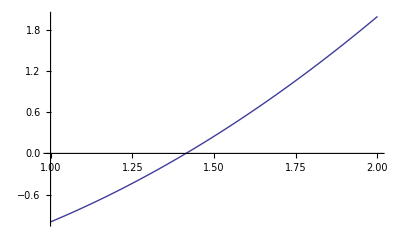

```mathematica
Plot[f[x],{x,1,2}]
```

```mathematica
Podem aplicar, per tant, el mètode de la Bisecció . Amb 100 iteracions:
```

```mathematica
Biseccio[f,{1,2,100}]
```

1.4142135623730950488

```mathematica
Mètode de Newton
```

```mathematica
Newton[f, x0, M] aplica el mètode de Newton a la funció f, agafant x0 com a valor inicial, i efectuant M iteracions.
```

```mathematica
Newton[f_,x0_,M_]:=Module[{xn},
xn=x0;
For[i=1, i≤M, i++,
xn=xn-f[xn]/f'[xn]
];
N[xn,20]
]
```

```mathematica
EXEMPLE: Calcularem una aproximació de la solució positiva de l'equació anterior( x^2-2=0)  aplicant el mètode de Newton amb 5 iteracions:
```

```mathematica
Newton[f,1,5]
```

1.4142135623730950488